```mathematica
Needs["VisualizeGenome`"]
Needs["BSFHistory`"]
```

```mathematica
convertGPATGenome[{"atan"["gauss"["plus"[0.2534219065387728 x0,4.630118948088606,-3.3017315841480586 x0,3.5686227847827148 x0],1]]}]
```

{ArcTan[ⅇ^(-(5.63012+0.520313 x0)^2)]}

```mathematica
listBSF["~/java/exp/GPAT3D_H_H2_200/run_001_132_GENOMES_MATH.txt"]//MatrixForm
```

(last
68945
68831
{times[times[times[plus[1.49998 times[x2,x0,x1,x1,times[1],1],5.32038,-0.185641 gauss[x1,x2,x2,1,x2],-1.09501 x1,2.30025 times[1,x1,x0,x2]],1],1]]}
0.990983)

```mathematica
(evo1=listBSFEvolution["~/java/exp/GPAT4D_E_200_NOREPEAT/run_001_165_GENOMES_MATH.txt"])//MatrixForm;
```

```mathematica
(evo1=listBSFEvolution["~/java/exp/GPAT4D_E_200_FULL/run_001_142_GENOMES_MATH.txt"])//MatrixForm
```

(1 | 12 | -1 | {plus} | 0.202532
2 | 172 | 12 | {plus[1.]} | 0.168421
3 | 290 | 172 | {plus[1. x3,0.896472 x1]} | 0.171252
4 | 369 | 290 | {times[x3,x1]} | 0.192771
5 | 460 | 369 | {times[x0,x1]} | 0.225352
6 | 552 | 460 | {times[x0,1]} | 0.318725
7 | 646 | 552 | {plus[1. times[x0,x3]]} | 0.192771
11 | 1077 | 978 | {plus[0.999902 times[x0,x3],1. x0]} | 0.295207
12 | 1198 | 1077 | {plus[0.999902 times[x0,x2],1. x0]} | 0.295207
20 | 1943 | 1852 | {plus[0.622019 times[x0,x0],1.06724 x0]} | 0.310869
22 | 2150 | 2042 | {plus[0.622019 times[x0,x2],1.06741 x0]} | 0.317574
23 | 2240 | 2150 | {plus[0.622019 plus[0.590037 x0,-3.63965 x2],1.06741 x0]} | 0.365033
27 | 2641 | 2541 | {plus[0.622019 times[x0,1],0.99731 x0]} | 0.396172
33 | 3237 | 3132 | {plus[0.430149 times[x0,1],0.99731 times[x0]]} | 0.374088
34 | 3397 | 3237 | {plus[0.430149 plus[2.19059 x0,0.0323691],0.99731 times[x0]]} | 0.424153
48 | 4790 | 4688 | {plus[0.414968 plus[3.12584 x0,-3.17074 x2],0.99731 times[x0]]} | 0.584525
80 | 7917 | 7817 | {plus[0.391209 plus[3.72722 x0,-2.89819 x2],0.871136 times[x0,x1]]} | 0.633386
176 | 17583 | 17493 | {times[plus[0.525394 plus[4.1923 x0,2.62223 x2],1.5027 times[x0,x1]]]} | 0.238138
457 | 45669 | 45557 | {times[times[plus[0.555793 plus[4.1392 x0,-1.97964 x2],1.49994 times[x0,x1]]]]} | 0.888889
816 | 81560 | 81468 | {times[times[plus[0.555793 plus[4.13824 x0,-1.97917 x2],1.49994 times[x0,x1]]]]} | 0.888889)

```mathematica
showAsExpressions[evo1]/.{x0->Subscript[x, 1],x1->Subscript[x, 2],x2->Subscript[x, 3],x3->Subscript[x, 4]}
```

Gen | Expression | Expanded | f
1 | {0} | {0} | 0.202532
2 | {1.} | {1.} | 0.168421
3 | {0.896472 x_2+1. x_4} | {0.896472 x_2+1. x_4} | 0.171252
4 | {x_2 x_4} | {x_2 x_4} | 0.192771
5 | {x_1 x_2} | {x_1 x_2} | 0.225352
6 | {x_1} | {x_1} | 0.318725
7 | {1. x_1 x_4} | {1. x_1 x_4} | 0.192771
11 | {1. x_1+0.999902 x_1 x_4} | {1. x_1+0.999902 x_1 x_4} | 0.295207
12 | {1. x_1+0.999902 x_1 x_3} | {1. x_1+0.999902 x_1 x_3} | 0.295207
20 | {1.06724 x_1+0.622019 x_1^2} | {1.06724 x_1+0.622019 x_1^2} | 0.310869
22 | {1.06741 x_1+0.622019 x_1 x_3} | {1.06741 x_1+0.622019 x_1 x_3} | 0.317574
23 | {1.06741 x_1+0.622019 (0.590037 x_1-3.63965 x_3)} | {1.43442 x_1-2.26393 x_3} | 0.365033
27 | {1.61933 x_1} | {1.61933 x_1} | 0.396172
33 | {1.42746 x_1} | {1.42746 x_1} | 0.374088
34 | {0.99731 x_1+0.430149 (0.0323691+2.19059 x_1)} | {0.0139235+1.93959 x_1} | 0.424153
48 | {0.99731 x_1+0.414968 (3.12584 x_1-3.17074 x_3)} | {2.29443 x_1-1.31576 x_3} | 0.584525
80 | {0.871136 x_1 x_2+0.391209 (3.72722 x_1-2.89819 x_3)} | {1.45812 x_1+0.871136 x_1 x_2-1.1338 x_3} | 0.633386
176 | {1.5027 x_1 x_2+0.525394 (4.1923 x_1+2.62223 x_3)} | {2.20261 x_1+1.5027 x_1 x_2+1.3777 x_3} | 0.238138
457 | {1.49994 x_1 x_2+0.555793 (4.1392 x_1-1.97964 x_3)} | {2.30054 x_1+1.49994 x_1 x_2-1.10027 x_3} | 0.888889
816 | {1.49994 x_1 x_2+0.555793 (4.13824 x_1-1.97917 x_3)} | {2.30001 x_1+1.49994 x_1 x_2-1.10001 x_3} | 0.888889

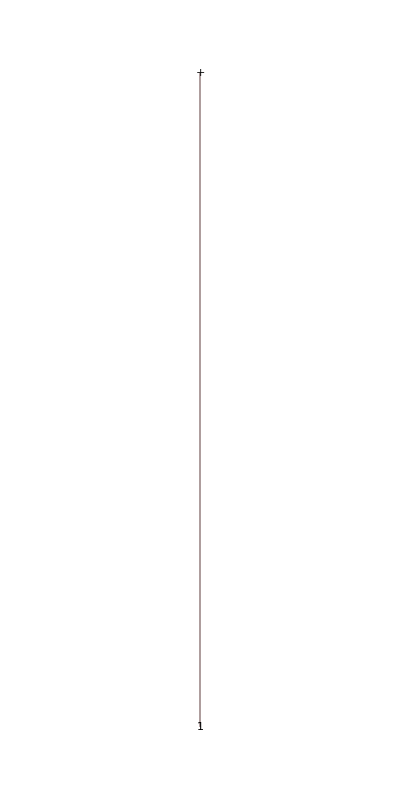
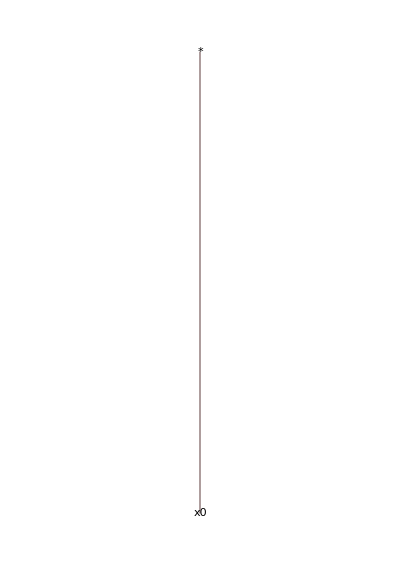
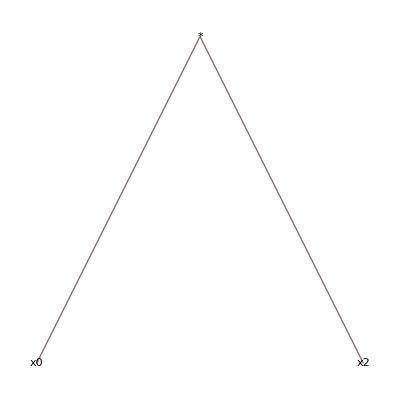
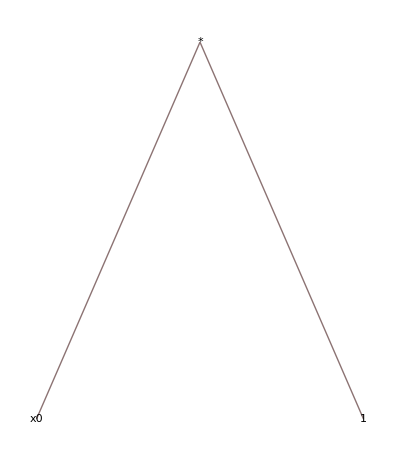
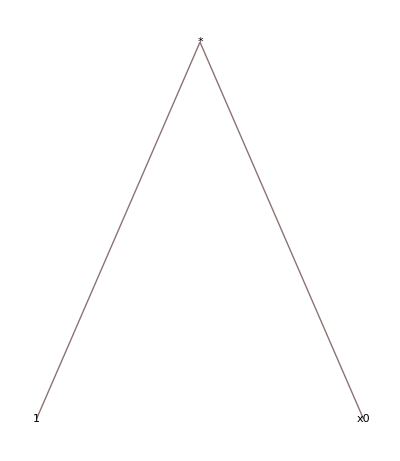
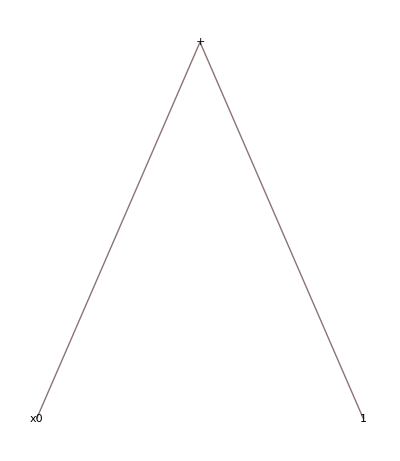
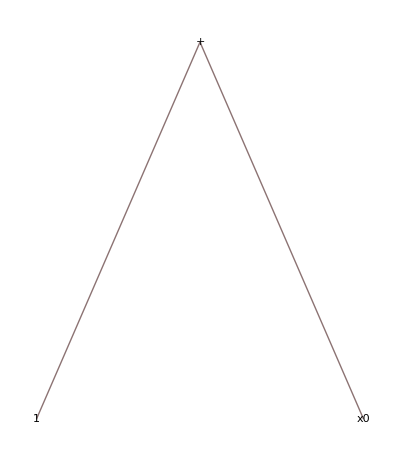
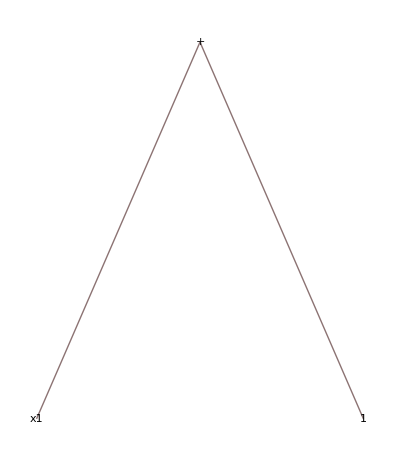
Gen | Genome | Sorted | Simplified | f
1 | -Graphics- | -Graphics- | -Graphics- | 0.202532
2 | -Graphics- | -Graphics- | -Graphics- | 0.169571
3 | -Graphics- | -Graphics- | -Graphics- | 0.318725
8 | -Graphics- | -Graphics- | -Graphics- | 0.192771
11 | -Graphics- | -Graphics- | -Graphics- | 0.318725
17 | -Graphics- | -Graphics- | -Graphics- | 0.115228
18 | -Graphics- | -Graphics- | -Graphics- | 0.155636
22 | -Graphics- | -Graphics- | -Graphics- | 0.183908
24 | -Graphics- | -Graphics- | -Graphics- | 0.192771
25 | -Graphics- | -Graphics- | -Graphics- | 0.198921
55 | -Graphics- | -Graphics- | -Graphics- | 0.491991
110 | -Graphics- | -Graphics- | -Graphics- | 0.11155
113 | -Graphics- | -Graphics- | -Graphics- | 0.204221
120 | -Graphics- | -Graphics- | -Graphics- | 0.416221
143 | -Graphics- | -Graphics- | -Graphics- | 0.197531
144 | -Graphics- | -Graphics- | -Graphics- | 0.175439
145 | -Graphics- | -Graphics- | -Graphics- | 0.207273
151 | -Graphics- | -Graphics- | -Graphics- | 0.216729
152 | -Graphics- | -Graphics- | -Graphics- | 0.219843
154 | -Graphics- | -Graphics- | -Graphics- | 0.219857
189 | -Graphics- | -Graphics- | -Graphics- | 0.22273
199 | -Graphics- | -Graphics- | -Graphics- | 0.198265
209 | -Graphics- | -Graphics- | -Graphics- | 0.2
212 | -Graphics- | -Graphics- | -Graphics- | 0.200376
213 | -Graphics- | -Graphics- | -Graphics- | 0.224577
273 | -Graphics- | -Graphics- | -Graphics- | 0.198265
278 | -Graphics- | -Graphics- | -Graphics- | 0.25
354 | -Graphics- | -Graphics- | -Graphics- | 0.258436
362 | -Graphics- | -Graphics- | -Graphics- | 0.141706
364 | -Graphics- | -Graphics- | -Graphics- | 0.177137
365 | -Graphics- | -Graphics- | -Graphics- | 0.198265
367 | -Graphics- | -Graphics- | -Graphics- | 0.198265
370 | -Graphics- | -Graphics- | -Graphics- | 0.198894
373 | -Graphics- | -Graphics- | -Graphics- | 0.241975
406 | -Graphics- | -Graphics- | -Graphics- | 0.278387
448 | -Graphics- | -Graphics- | -Graphics- | 0.279236
487 | -Graphics- | -Graphics- | -Graphics- | 0.281367
517 | -Graphics- | -Graphics- | -Graphics- | 0.281641
537 | -Graphics- | -Graphics- | -Graphics- | 0.409198
553 | -Graphics- | -Graphics- | -Graphics- | 0.484098
557 | -Graphics- | -Graphics- | -Graphics- | 0.498831
559 | -Graphics- | -Graphics- | -Graphics- | 0.534893
562 | -Graphics- | -Graphics- | -Graphics- | 0.58395
570 | -Graphics- | -Graphics- | -Graphics- | 0.795964
629 | -Graphics- | -Graphics- | -Graphics- | 0.841682
725 | -Graphics- | -Graphics- | -Graphics- | 0.951961

```mathematica
showGenomes[evo1]
```

```mathematica
Export["GPAT_H_RUN66.pdf",%]
```

GPAT_H_RUN66.pdf

## 1 D Regression

```mathematica
(evo1=listBSFEvolution["~/java/exp/GPAT1D_G_2/run_001_174_GENOMES_MATH.txt"])//MatrixForm
```

(1 | 17300193 | -1 | {plus} | 2.70569×10^-8
2 | 17300336 | 17300193 | {plus[0.987404]} | 2.70621×10^-8
3 | 17300444 | 17300336 | {plus[0.987404 gauss[1]]} | 2.70588×10^-8
4 | 17300545 | 17300444 | {plus[0.987404 times[1]]} | 2.70621×10^-8
5 | 17300618 | 17300545 | {gauss[plus[0.987404 gauss[1],1.]]} | 2.70577×10^-8
7 | 17300852 | 17300767 | {gauss[plus[0.987404 gauss[1],0.549582,1.3494 x0]]} | 2.70569×10^-8
11 | 17301246 | 17301143 | {gauss[plus[1.82938 gauss[1],-0.878784,4.25122 x0],1]} | 2.70569×10^-8
12 | 17301371 | 17301246 | {times[plus[1.21817 gauss[1],-0.878784,4.24779 x0],1]} | 2.70898×10^-8
14 | 17301559 | 17301465 | {times[plus[1.25431 times[1],-0.865015,4.26333 x0],1]} | 2.70943×10^-8
18 | 17301970 | 17301829 | {times[plus[1.25431 times[1],0.0519364,4.26333 x0],1,x0]} | 2.89265×10^-8
19 | 17302043 | 17301970 | {times[plus[1.25431 times[1,x0],0.052181,4.26333 x0],1,x0]} | 2.94957×10^-8
20 | 17302151 | 17302043 | {times[plus[1.25431 times[1,x0,x0],-0.837428,3.78246 x0],x0,x0]} | 7.4362×10^-7
21 | 17302253 | 17302151 | {times[plus[1.25431 times[1,x0,x0],-0.837428,3.78246 x0],x0,x0,1]} | 7.4362×10^-7
131 | 17313195 | 17313076 | {times[times[plus[1.49973 times[1,x0,x0],-1.14579,2.34657 x0],x0,x0,1]]} | 0.0110484
192 | 17319347 | 17319239 | {plus[1. times[times[plus[1.49986 times[1,x0,x0],-1.15417,2.347 x0],x0,x0,1]]]} | 0.0111279
202 | 17320363 | 17320266 | {plus[1. times[times[plus[1.49986 times[1,x0,x0],-1.15417,2.347 x0],x0,x0,1]],1. x0]} | 0.0120525
362 | 17336319 | 17336198 | {plus[1. times[times[plus[1.49986 times[1,x0,x0],-1.13829,2.32155 x0],x0,x0,1],1],2.1781 x0]} | 0.0388955
428 | 17342956 | 17342831 | {plus[1. times[times[plus[1.49986 times[1,x0,x0],-1.15575,2.29732 x0],x0,x0,1],1],3.93559 x0,1.00118]} | 0.0620225
977 | 17397784 | 17397676 | {plus[1.00023 times[times[plus[1.49986 times[1,x0,x0],-1.11949,2.29902 x0],x0,x0,1],1],3.72859 x0,-4.18753]} | 0.956232)

```mathematica
targetG=1.5*x0^4+2.3*x0^3-1.1*x0^2+3.7*x0-4.5
```

-4.5+3.7 x0-1.1 x0^2+2.3 x0^3+1.5 x0^4

```mathematica
fitness[target_,evolved_]:=
(1/(1+Mean[Table[(target-evolved)^2,{x0,-10,10,20/19}]]))
```

```mathematica
Grid[{Simplify[convertGPATGenome[#][[1]]],
fitness[targetG,convertGPATGenome[#][[1]]]}&/@evo1[[All,4]]]
```

0 | 2.70569×10^-8
0.987404 | 2.70621×10^-8
0.363246 | 2.70588×10^-8
0.987404 | 2.70621×10^-8
0.155916 | 2.70577×10^-8
ⅇ^(-1. (0.912827+1.3494 x0)^2) | 2.70569×10^-8
ⅇ^(-1. (0.794206+4.25122 x0)^2) | 2.70569×10^-8
-0.430645+4.24779 x0 | 2.70898×10^-8
0.38929+4.26333 x0 | 2.70943×10^-8
x0 (1.30624+4.26333 x0) | 2.89265×10^-8
x0 (0.052181+5.51763 x0) | 2.94957×10^-8
x0^2 (-0.837428+3.78246 x0+1.25431 x0^2) | 7.4362×10^-7
x0^2 (-0.837428+3.78246 x0+1.25431 x0^2) | 7.4362×10^-7
x0^2 (-1.14579+2.34657 x0+1.49973 x0^2) | 0.0110484
1. x0^2 (-1.15417+2.347 x0+1.49986 x0^2) | 0.0111279
x0 (1.-1.15417 x0+2.347 x0^2+1.49986 x0^3) | 0.0120525
x0 (2.1781-1.13829 x0+2.32155 x0^2+1.49986 x0^3) | 0.0388955
1.00118+3.93559 x0-1.15575 x0^2+2.29732 x0^3+1.49986 x0^4 | 0.0620225
-4.18753+3.72859 x0-1.11974 x0^2+2.29954 x0^3+1.5002 x0^4 | 0.956232

```mathematica
Manipulate[{fitness[targetG,convertGPATGenome[evo1[[i,4]]][[1]]],Plot[{targetG,convertGPATGenome[evo1[[i,4]]][[1]]},{x0,-10,10},PlotRange->{-150,150},PlotStyle->Thick]},{i,1,Length[evo1],1}]
```